=========================================

任务二：简单受迫振动分析

=========================================

=== 2.1 稳态响应与共振曲线 ===

稳态振幅函数 A(omega) 已建立。

计算结果：

共振频率 (Resonance Frequency): omega = 0.9899

最大振幅 (Max Amplitude): A_max = 5.025

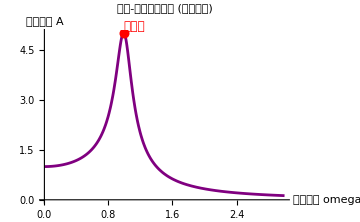

=== 2.2 数值求解 (NDSolve) 与过渡过程观察 ===

--------------------------------

频率 omega = 0.5

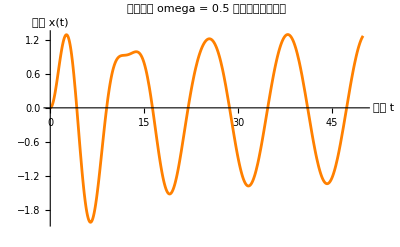

观察：可以看到前几秒振幅不稳定（瞬态），之后趋于稳定的余弦振动。

--------------------------------

频率 omega = 1.

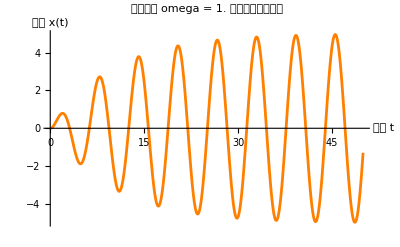

观察：可以看到前几秒振幅不稳定（瞬态），之后趋于稳定的余弦振动。

--------------------------------

频率 omega = 1.5

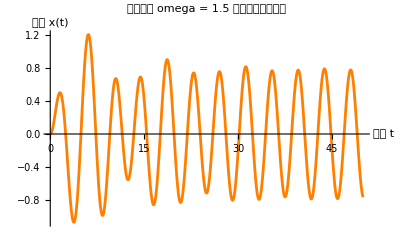

观察：可以看到前几秒振幅不稳定（瞬态），之后趋于稳定的余弦振动。

任务二全部完成。

```mathematica
(* =================================================*)(*任务二：简单受迫振动*)(* =================================================*)Print["\n\n========================================="];
Print["任务二：简单受迫振动分析"];
Print["========================================="];

Clear["Global`*"] (*再次清空，防止任务一的变量干扰*)

(*参数定义*)
m=1;k=1;gamma=0.2;F0=1;

(*-------2.1 稳态响应分析-------*)
Print["\n=== 2.1 稳态响应与共振曲线 ==="];

(*思路笔记：受迫振动的稳态解形式为 x(t)=A cos(omega*t-phi) 根据课本推导（或直接解方程取特解），振幅 A 的公式如下：A(omega)=F0/Sqrt[(k-m*omega^2)^2+(gamma*omega)^2]*)

(*定义振幅函数*)
Amp[w_]:=F0/Sqrt[(k-m*w^2)^2+(gamma*w)^2];

Print["稳态振幅函数 A(omega) 已建立。"];

(*寻找共振频率和最大振幅*)
(*之前想用求导算，后来发现 Maximize 函数可以直接算出最大值，太方便了*)
maxRes=Maximize[{Amp[w],0<=w<=3},w];
maxAmp=maxRes[[1]]; (*最大值*)
resFreq=w/. maxRes[[2]]; (*对应的 omega*)

Print["计算结果："];
Print["共振频率 (Resonance Frequency): omega = ",NumberForm[resFreq,4]];
Print["最大振幅 (Max Amplitude): A_max = ",NumberForm[maxAmp,4]];

(*绘制共振曲线*)
(*Epilog 用来在图上标记那个特殊的点，显得很专业*)
plotRes=Plot[Amp[w],{w,0,3},AxesLabel->{"驱动频率 omega","稳态振幅 A"},PlotLabel->"振幅-频率响应曲线 (共振曲线)",PlotStyle->Purple,Epilog->{Red,PointSize[0.02],Point[{resFreq,maxAmp}],Text[Style["共振点",12,Red],{resFreq,maxAmp},{-1.2,-1}]},ImageSize->Medium];

Print[plotRes];

(*-------2.2 数值求解与过渡过程-------*)
Print["\n=== 2.2 数值求解 (NDSolve) 与过渡过程观察 ==="];

(*定义驱动方程*)
(*注意：这里 eqn2 里面用了具体的数值，方便 NDSolve 处理*)
eqn2[w_]:=m*x''[t]+gamma*x'[t]+k*x[t]==F0*Cos[w*t];
ic={x[0]==0,x'[0]==0};

(*需要观察的三个频率*)
omegas={0.5,1.0,1.5};

(*循环求解并绘图*)
(*这里用 Table 遍历三个频率，比写三遍代码要简洁*)
Do[currentW=omegas[[i]];
(*数值求解*)solNum=NDSolveValue[{eqn2[currentW],ic},x[t],{t,0,50}];
(*绘图*)p=Plot[solNum,{t,0,50},PlotRange->All,PlotLabel->StringForm["驱动频率 omega = `` 的瞬态到稳态过程",currentW],AxesLabel->{"时间 t","位移 x(t)"},PlotStyle->Orange];
Print["--------------------------------"];
Print["频率 omega = ",currentW];
Print[p];
Print["观察：可以看到前几秒振幅不稳定（瞬态），之后趋于稳定的余弦振动。"];,{i,1,3}];

Print["\n任务二全部完成。"];
```